```mathematica
k=200;
```

```mathematica
costfunction[board_,weight_]:=Module[{team1,team2,zeroes,cost,me,min1,min2,cf},
(*team1=Position[board,1];
team2=Position[board,2];
zeroes=Position[board,0];
cf=Table[
me=PS[[jj]];
If[Length[team1]>0,
min1=Min[Table[Norm[me-team1[[m]]],{m,1,Length[team1]}]];
,
min1=0
];
If[Length[team2]>0,
min2=Min[Table[Norm[me-team2[[m]]],{m,1,Length[team2]}]];
,
min2=0
];
If[min1<min2,weight[[me[[1]]]][[me[[2]]]],If[min1>min2,-weight[[me[[1]]]][[me[[2]]]],0.]]
,{jj,1,Length[PS]}];
Return[Total[cf]];*)
COMPUTER=Position[board,1];
HUMAN=Position[board,2];
PTS=Nearest[Position[board,_?(#>0&)]];
cf=Total[Flatten[Table[
Table[
near=PTS[{i,j}];
If[Length[near]==2,
0,
near=near[[1]];
If[MemberQ[COMPUTER,near]==True,
weight[[near[[1]],near[[2]]]]
,
-weight[[near[[1]],near[[2]]]]
]
]
,{j,1,10}]
,{i,1,10}]]];
Return[cf];
]
```

### YOU GO FIRST

### Monte Carlo Tree Search

```mathematica
(*grid=10;*)
grid=10;
TotalArea= grid^2;
board=Table[0,{grid},{grid}];
PS=Position[board,0];
weight=Table[1,{i,1,grid},{j,1,grid}];
(*weight=Table[1,{i,1,grid},{j,1,grid}];*)
```

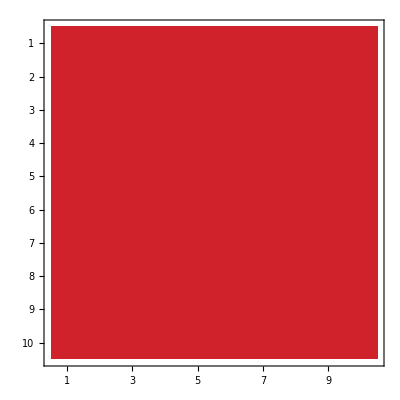

```mathematica
MatrixPlot[weight,ColorFunction->"TemperatureMap"]
```

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;7]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,3}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,4,7}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

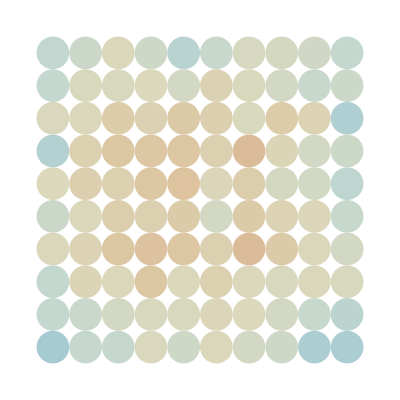

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

### Your Move

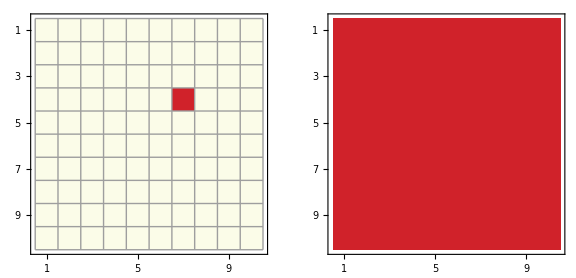

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

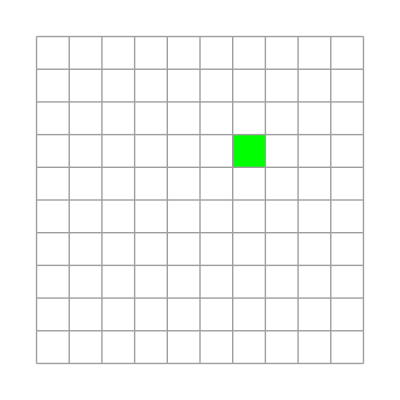

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
board[[6]][[6]]
```

0

```mathematica
board[[6]][[6]]=2
```

2

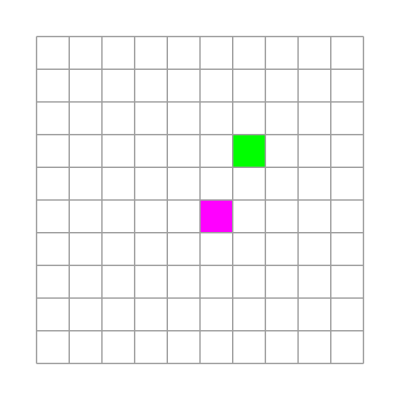

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

-20

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;5]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,2}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,3,5}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Green,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{Magenta,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

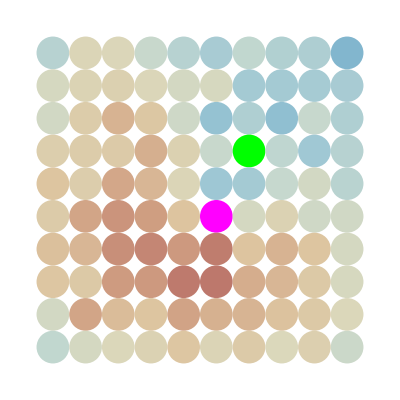

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

### Your Move

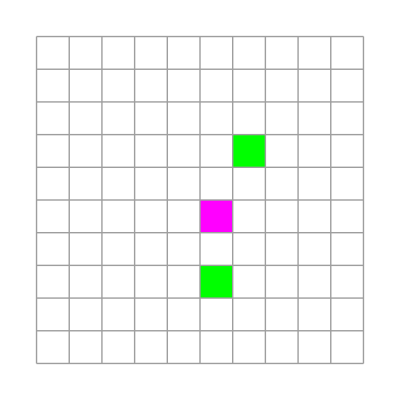

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

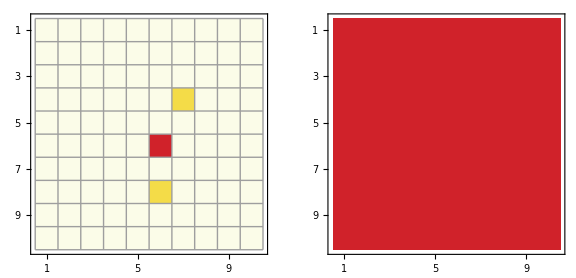

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[3]][[7]]
```

0

```mathematica
board[[3]][[7]]=2
```

2

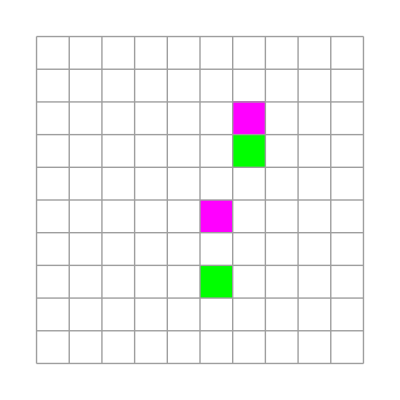

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

-5

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;3]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,1}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,2,3}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Green,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{Magenta,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

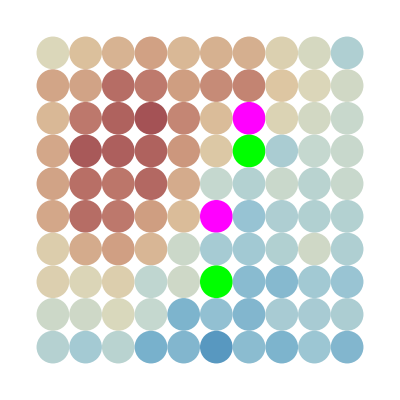

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

### Your Move

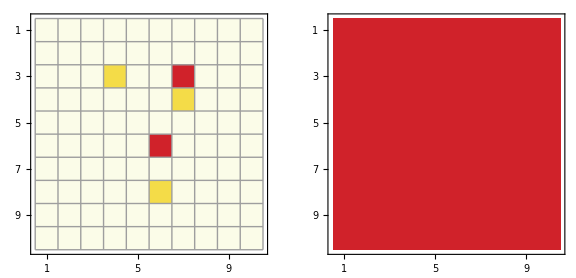

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[7]][[3]]
```

0

```mathematica
board[[7]][[3]]=2
```

2

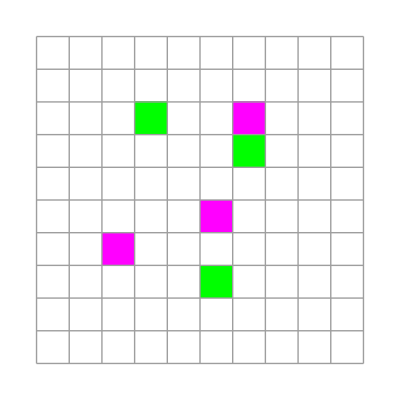

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

9

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;1]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,1,1}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Green,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{Magenta,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

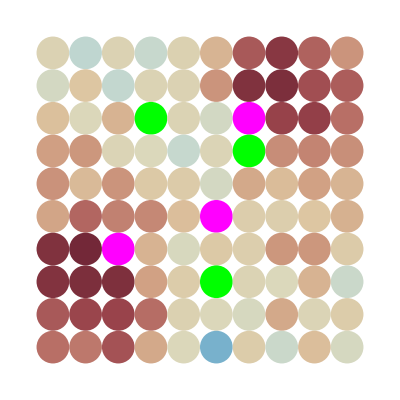

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

### Your Move

```mathematica
boardT=board;
```

```mathematica
board=boardT;
```

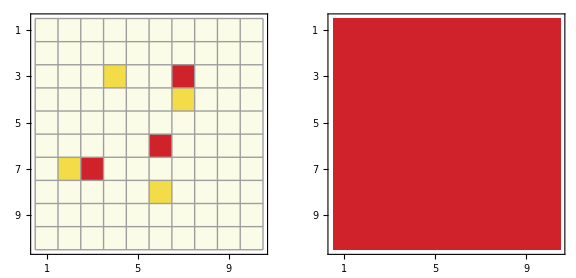

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[8]][[7]]
```

0

```mathematica
(*board[[6]][[4]]=2*)
board[[8]][[7]]=2
```

2

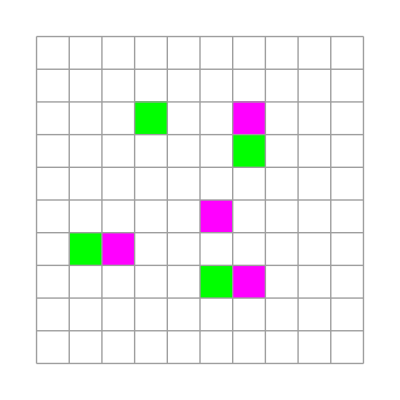

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
finalscore=costfunction[board,weight];
```

```mathematica
finalscore
```

2

```mathematica
If[finalscore>0,Print[Style["MACHINE>MAN",Black,100]],Print[Style["MAN>MACHINE",Black,100]];
]
```

MACHINE>MAN

```mathematica
finalscore
```

2

### blah

```mathematica
COMPUTER=Position[board,1];
HUMAN=Position[board,2];
```

```mathematica
PTS=Nearest[Position[board,_?(#>0&)]];
```

```mathematica
Total[Flatten[Table[
Table[
near=PTS[{i,j}];
If[Length[near]==2,
0,
near=near[[1]];
If[MemberQ[COMPUTER,near]==True,
-weight[[near[[1]],near[[2]]]]
,
weight[[near[[1]],near[[2]]]]
]
]
,{j,1,10}]
,{i,1,10}]]]
```

-2

```mathematica
MemberQ[COMPUTER,near]
```

False

```mathematica
COMPUTER
```

{{3,4},{4,7},{7,2},{8,6}}

```mathematica
board=Table[0,{10},{10}];
```

```mathematica
board[[1,1]]=0;
board[[8,3]]=1;
board[[2,2]]=0;
```